```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
```

```mathematica
minTerminalVilliRadius=25mkm;
maxTerminalVilliRadius=80mkm;
maxNonStemVilliRadius=300mkm;
areaFunc[radius_]:=π (radius/mkm)^2;
```

```mathematica
sectionName="2274";

curDir=NotebookDirectory[];
statFile="E:\\06_New cuts of the first sections\\"<>sectionName<>"\\results\\_"<>sectionName<>"_Total_Villous_regions_statistics.csv";



data01=Import[statFile,"Table",FieldSeparators->";"];
dataNames=data01[[1]];
data02=data01[[2;;-1]];
```

```mathematica
data01//Dimensions;
data02//Dimensions;
dataNames
```

{Villous region number,Surface (ÂµmÂ.b2),Perimeter (Âµm),Perimeter_contact (Âµm),Perimeter_frame (Âµm),Nb_IVS_Inside_Region,IVS_Area_Inside_Region (ÂµmÂ.b2),IVS_Perimeter_Inside_Region (Âµm),Nb_Fetal_Capillaries_Inside,Fetal_Capillaries_Area_Inside (ÂµmÂ.b2),FetalCapillariesPerimeter (Âµm)}

```mathematica
areaData=data02[[;;,2]];
```

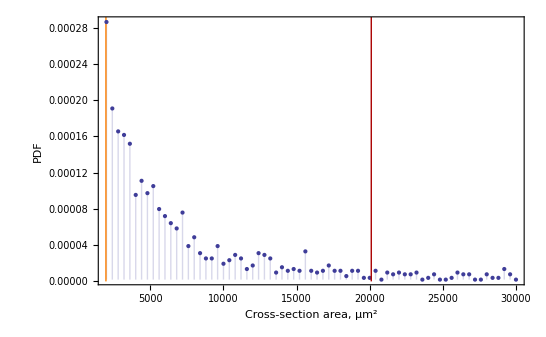

```mathematica
intervalOfInterest={2000,areaFunc[maxTerminalVilliRadius]*1.5};
selectedAreaData=Select[areaData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
areaBinSize={400};
distribArea=HistogramDistribution[selectedAreaData,areaBinSize];
pdfArea=PDF[distribArea,s];

pdfAreaHistogramPlot=DiscretePlot[pdfArea,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],areaBinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}];
Show[pdfAreaHistogramPlot,
Graphics[{
{Orange,Line[{{areaFunc[minTerminalVilliRadius],0},{areaFunc[minTerminalVilliRadius],0.0004}}]},
{Darker[Red],Line[{{areaFunc[maxTerminalVilliRadius],0},{areaFunc[maxTerminalVilliRadius],0.0004}}]},
{Darker[Green],Line[{{areaFunc[maxNonStemVilliRadius],0},{areaFunc[maxNonStemVilliRadius],0.0004}}]}
}
]]

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

```mathematica
(* Plotting the histogram of the villous cross-sectional area logarithm *)
```

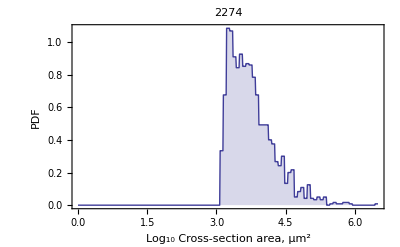

```mathematica
intervalOfInterest={10^0,∞};
selectedAreaData=Select[areaData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
logAreaData=Log[10,selectedAreaData];
logBinSize=0.07;
distribLogArea=HistogramDistribution[logAreaData,{logBinSize}];
pdfLogArea=PDF[distribLogArea,s];
distribLogAreaTempList=HistogramList[logAreaData,{logBinSize},"PDF"];
binsCenters=Table[(distribLogAreaTempList[[1,i]]+distribLogAreaTempList[[1,i+1]])/2,{i,1,Length[distribLogAreaTempList[[1]]]-1}];
distribLogAreaList=Transpose[{binsCenters,distribLogAreaTempList[[2]]}];

pdfLogAreaHistogramPlot= DiscretePlot[pdfLogArea,{s,Log[10,intervalOfInterest[[1]]],6.5,0.01},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Log_10 Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName];

Show[pdfLogAreaHistogramPlot,
Graphics[{
{Orange,Line[{{Log10[areaFunc[minTerminalVilliRadius]],0},{Log10[areaFunc[minTerminalVilliRadius]],0.0004}}]},
{Darker[Red],Line[{{Log10[areaFunc[maxTerminalVilliRadius]],0},{Log10[areaFunc[maxTerminalVilliRadius]],0.0004}}]},
{Darker[Green],Line[{{Log10[areaFunc[maxNonStemVilliRadius]],0},{Log10[areaFunc[maxNonStemVilliRadius]],0.0004}}]}
}
]]

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

```mathematica
(* Obtaining histogram points *)

distribAreaTempList=HistogramList[selectedAreaData,areaBinSize,"PDF"];
binsCenters=Table[(distribAreaTempList[[1,i]]+distribAreaTempList[[1,i+1]])/2,{i,1,Length[distribAreaTempList[[1]]]-1}];
distribAreaList=Transpose[{binsCenters,distribAreaTempList[[2]]}];
```

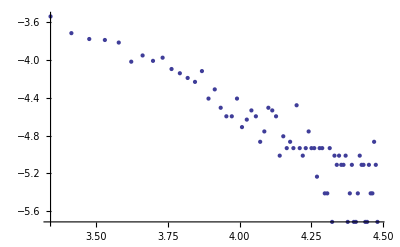

```mathematica
ListLogLogPlot[distribAreaList,PlotRange->All];
ListPlot[Log10[distribAreaList],PlotRange->(*{Automatic,{-4,-2.0}}*)All]
```

{A1→-104.184,A2→-2.46408×10^11}

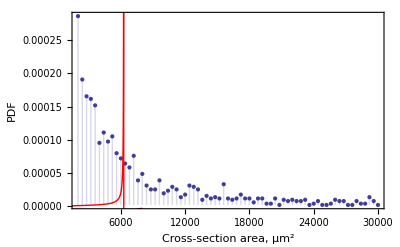

```mathematica
(* Fitting surface distribution *)

fitFunc=A1 s/(A2+s^3);
fitParams={A1,{A2,2*300^3}};
fitVars={s};
fitResult=FindFit[distribAreaList,fitFunc,fitParams,fitVars]

Show[
pdfAreaHistogramPlot,
(*ListPlot[distribLogAreaList,AxesOrigin->{0,0}],*)
Plot[Evaluate[fitFunc/.fitResult],{s,0*0.95*distribAreaList[[1,1]],8000},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red]
]
```

```mathematica
(* A histogram of the distribution of the logarithm of area *)
intervalOfInterest={10^0,∞};
selectedAreaData=Select[areaData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
logAreaData=Log[10,selectedAreaData];
logBinSize=0.07;
distribLogArea=HistogramDistribution[logAreaData,{logBinSize}];
pdfLogArea=PDF[distribLogArea,s];
distribLogAreaTempList=HistogramList[logAreaData,{logBinSize},"PDF"];
binsCenters=Table[(distribLogAreaTempList[[1,i]]+distribLogAreaTempList[[1,i+1]])/2,{i,1,Length[distribLogAreaTempList[[1]]]-1}];
distribLogAreaList=Transpose[{binsCenters,distribLogAreaTempList[[2]]}];

pdfLogAreaHistogramPlot= DiscretePlot[pdfLogArea,{s,Log[10,intervalOfInterest[[1]]],6.5,0.01},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Log_10 Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
```

-Graphics-

{A1→0.735406,A2→0.7,σ1→0.294845,σ2→0.701496,y1→1.1829,y2→3.4}

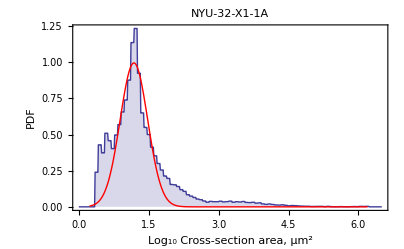

```mathematica
(* Fitting logarithm of surface distribution with two Gaussian *)
fittingInterval={0.8,1.8};
fittingData=Select[distribLogAreaList,#[[1]]>=fittingInterval[[1]]&&#[[1]]<=fittingInterval[[2]]&];


fitFunc={A1/(√(2π σ1^2))Exp[-(y-y1)^2/(2 σ1^2)](*+A1/(√(2π σ2^2))Exp[-(y-y2)^2/(2 σ2^2)]*),{A1>0,σ2>0}};
fitParams={{A1,0.7},{A2,0.7},{σ1,0.3},{σ2,0.7},{y1,2.0},{y2,3.4}};
fitVars={y};
fitResult=FindFit[fittingData,fitFunc,fitParams,fitVars]

Show[
pdfLogAreaHistogramPlot,
(*ListPlot[distribLogAreaList,AxesOrigin->{0,0}],*)
Plot[Evaluate[fitFunc/.fitResult],{y,0.6*distribLogAreaList[[1,1]],distribLogAreaList[[-1,1]]},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red](*,(*AxesOrigin->{0,0},*)PlotRange->All*)
]
```